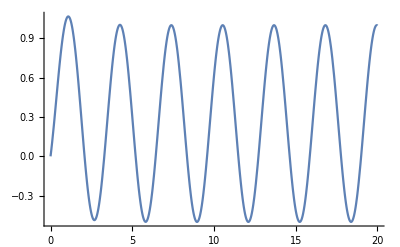

```mathematica
Plot[-0.45Cos[2t]+0.6Sin[2t]+0.25+0.2Exp[-t],{t,0,20}, PlotRange->All]
```

```mathematica
s=DSolve[{2x''[t]+x[t]==3Cos[0.7t],x[0]==1,x'[0]==0}, x[t],t]
```

{{x[t]→149.246 (-0.99835 Cos[0.707107 t]+1. Cos[0.00710678 t] Cos[0.707107 t]+0.00505063 Cos[0.707107 t] Cos[1.40711 t]+1. Sin[0.00710678 t] Sin[0.707107 t]+0.00505063 Sin[0.707107 t] Sin[1.40711 t])}}

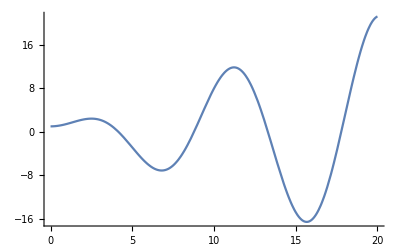

```mathematica
b=Plot[Evaluate[x[t]/. s],{t,0,20}, PlotRange->All]
```

```mathematica
Clear[x];
h=DSolve[{4x''[t]+9x[t]==Sin[1.5t], x[0]==1, x'[0]==0}, x[t], t]
```

{{x[t]→-0.0833333 (-12. Cos[1.5 t]+1. t Cos[1.5 t]-0.333333 Sin[1.5 t]+0.333333 Cos[3. t] Sin[1.5 t]-0.333333 Cos[1.5 t] Sin[3. t])}}

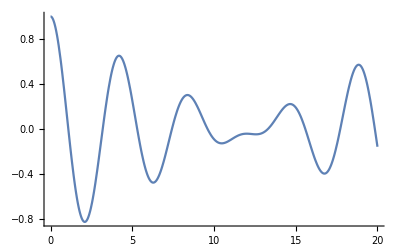

```mathematica
c=Plot[Evaluate[x[t] /. h], {t,0,20}, PlotRange->All]
```